```mathematica
b[T_]:=(16 G^2)/(π α)(2+Cos[w]^2)(7 π^2 T^5)/120;
Ω[M_,T_,θ_]:=√(θ^2/((1+(6T)/M b[T])^2+θ^2));
α=1/30;
w=30/180 π;
G=1/(300000)^2;
```

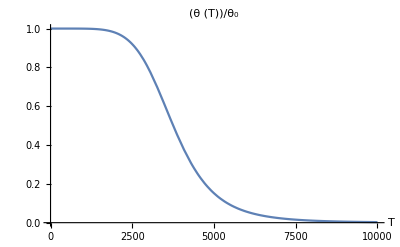

```mathematica
Block[{M,θ},
M=500;θ=10^-5;
Plot[Ω[M,T,θ]/θ,{T,0,10^4},AxesLabel->Automatic,PlotRange->All,PlotLabel->"(θ (T))/θ_0",AxesLabel->{"Temperature, MeV","θ(T)/θ_0"}]
]
```

```mathematica
Plot3D[Ω[m,T,θ]/θ/.θ->10^-5,{T,0,10^4},{m,100,500},PlotLabel->"(θ (T))/θ_0",AxesLabel->{"Temperature, MeV","Mass, MeV","θ(T)/θ_0"}]
```

-Graphics3D-

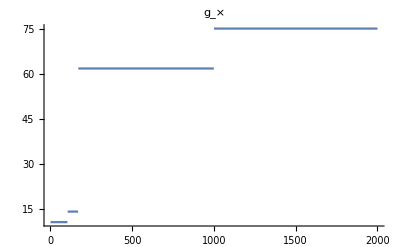

```mathematica
g[T_]:=Piecewise[{{10.75,T≤105},{14.25,T≤170},{61.75,T≤ 1000},{75,True}},T];
Plot[g[T],{T,1,2000},PlotRange->All,PlotLabel->"g_×"]
Subscript[M, pl][T_]:=(1.22 10^22)/(1.66 √g[T]);
γ[T_]:=G^2 θ^2 Subscript[M, pl][T];
```

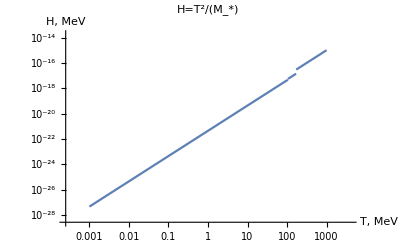

```mathematica
LogLogPlot[T^2/(Subscript[M, pl][T]),{T,1000,0.001},PlotLabel->"H=T^2/(M_*)",AxesLabel->{"T, MeV","H, MeV"},GridLines->{{0.07,3},{}}]
```

```mathematica
Manipulate[Block[{θ},(
θ=10^x;

RegionPlot[{
(m≥y T && m^2<1/(γ[T]T))/.T->10^t,
(1/y T<m<y T&&m^2<1/(γ[T]T)&&T^3 Subscript[M, pl][T]<1/(G^2 θ^2))/.T->10^t,
(m≤ 1/y T&&T^3 Subscript[M, pl][T]<1/(G^2 θ^2))/.T->10^t
},{m,1,500},{t,4,-3},PlotLabel->"Decoupling particles",FrameLabel->{"Mass, MeV","log_10(T), MeV"},PlotLegends->{"Non-relativistic","Intermediate","Relativistic"},GridLines->{{135,490},{}}]
)],{{x,-4,"log(θ)"},-10,0,1,Appearance->"Labeled"},{{y,5,"regime factor"},1,10,1,Appearance->"Labeled"}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["decoupling_regimes_10^-2.png",DynamicModule[{x=-2,y=5},θ=10^x;RegionPlot[{m≥y T&&m^2<1/(γ[T] T)/.T->10^t,T/y<m<y T&&m^2<1/(γ[T] T)&&T^3 Subscript[M, pl][T]<1/(G^2 θ^2)/.T->10^t,m≤T/y&&T^3 Subscript[M, pl][T]<1/(G^2 θ^2)/.T->10^t},{m,1,500},{t,4,-3},PlotLabel->"Decoupling particles",FrameLabel->{"Mass, MeV","\!\(\*SubscriptBox[\(log\), \(10\)]\)(T), MeV"},PlotLegends->{"Non-relativistic","Intermediate","Relativistic"},GridLines->{{135,490},{}}]]]
```

/Users/b/Repositories/BBN/pyBBN/src/notes/images

decoupling_regimes_10^-2.png

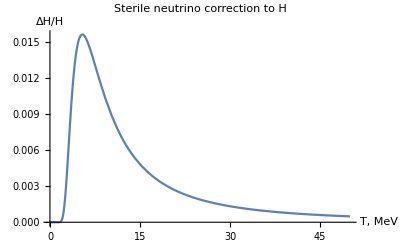

```mathematica
Plot[7/32 Γ[m](g[T]/g[Subscript[T, N]])^(4/3)E^(-(Γ[m]Subscript[M, pl][T])/(2 T^2))*(Subscript[M, pl][T])/T^2/.θs[3]/.{m->300,Subscript[T, N]->1000},{T,0.01,50},PlotLabel->"Sterile neutrino correction to H",AxesLabel->{"T, MeV","ΔH/H"},PlotRange->All]
```